```mathematica
(*ClearAll["Global`*"]*)
(*DumpSave[NotebookDirectory[]<>"integratorsols1000.mx", "Global`"];*)
```

```mathematica
Get[NotebookDirectory[]<>"integratorsols1000.mx"]
```

## Data Import and Integration

### Constants definition

```mathematica
(* Constants in cgs*)
wp=MachinePrecision;
G=6.67*10^-8;
msun=2*10^33;
rsun=7*10^10;
au=1.5*10^13;
pc=3*10^18;
kpc=3*10^21;
yr=3*10^7;
kb = 1.4 * 10^-16;
mp = 1.7 * 10^-24;

(* All masses initialized in Msun *)
Subscript[m, bulge]=3.76* 10^9 msun;
Subscript[m, disk]=6.0* 10^10 msun;
Subscript[m, halo]=1.0* 10^12 msun;
Subscript[m, hole]=4.0* 10^6 msun;

(* All distances initialized in AU  *)
Subscript[r, halo] = 4.125* 10^9 au;

(* Bulge and disk parameters *)
Subscript[a, b]=2.0* 10^7 au;
Subscript[a, d]=5.7* 10^8 au;
Subscript[b, d]=6.2* 10^7 au;

(* Cluster parameters *)
rc=206265au;

(* Maximum time *)
max=10^10 yr;
```

```mathematica
(* Force definitions *)
Subscript[F, hole][r_, coord_] = (-G*Subscript[m, hole]*coord)/r^3;
Subscript[F, bulge][r_, coord_] = (-G*Subscript[m, bulge]*coord)/(r^2(Subscript[a, b]+r));
Subscript[F, cluster][r_, coord_]= (-2*G*Subscript[m, hole] * coord)/(Max[rc,r] * r^2);
Subscript[F, disk][r_, coord_, ρ_, zbd_ ] = (-G*Subscript[m, disk]* coord)/((ρ^2+(Subscript[a, d]+zbd)^2)^1.5);
Subscript[F, halo][r_, coord_]= -G*Subscript[m, halo]*coord*(Log[1+r/Subscript[r, halo]]/r^3-1/(r^2*(r+Subscript[r, halo])));
```

### Import and Integration

```mathematica
data = Import[NotebookDirectory[]<>"data1000.json", "RawJSON"];
irange=Length[data];
jranges = Table[0,irange];
Do[jranges = ReplacePart[jranges, i -> Length[data⟦i⟧["x"]]], 
{i, irange}];
solutions = Table[0,irange];
endtimes = Table[0,irange];
```

```mathematica
Do[ solutions=ReplacePart[solutions, i -> Table[0,jranges⟦i⟧]];
endtimes=ReplacePart[endtimes, i -> Table[0,jranges⟦i⟧]],
{i,irange}]

Off[NDSolve::mxst]
fi = 0;
ProgressIndicator[Dynamic[fi], {1,Length@Flatten[solutions]}]
Do[
x0= data⟦i⟧["x"]⟦j⟧;
y0= data⟦i⟧["y"]⟦j⟧;
z0=data⟦i⟧["z"]⟦j⟧;
vx0= data⟦i⟧["vx"]⟦j⟧;
vy0= data⟦i⟧["vy"]⟦j⟧;
vz0= data⟦i⟧["vz"]⟦j⟧;

eqn = {x''[t] == Subscript[F, hole][r,x[t]] + Subscript[F, bulge][r,x[t]] + Subscript[F, cluster][r,x[t]] + Subscript[F, disk][r,x[t],ρ,zbd] + Subscript[F, halo][r,x[t]]/.{r-> Sqrt[x[t]^2+y[t]^2+z[t]^2], ρ-> Sqrt[x[t]^2+y[t]^2], zbd -> Sqrt[z[t]^2+Subscript[b, d]^2]},
y''[t] ==  Subscript[F, hole][r,y[t]] + Subscript[F, bulge][r,y[t]] + Subscript[F, cluster][r,y[t]] + Subscript[F, disk][r,y[t],ρ,zbd] + Subscript[F, halo][r,y[t]]/.{r-> Sqrt[x[t]^2+y[t]^2+z[t]^2], ρ-> Sqrt[x[t]^2+y[t]^2], zbd -> Sqrt[z[t]^2+Subscript[b, d]^2]},
z''[t] ==  Subscript[F, hole][r,z[t]] + Subscript[F, bulge][r,z[t]] + Subscript[F, cluster][r,z[t]] + Subscript[F, disk][r,z[t],ρ,zbd] + Subscript[F, halo][r,z[t]]/.{r-> Sqrt[x[t]^2+y[t]^2+z[t]^2], ρ-> Sqrt[x[t]^2+y[t]^2], zbd -> Sqrt[z[t]^2+Subscript[b, d]^2]}, x[0]==x0, y[0]==y0, z[0]==z0, x'[0]== vx0, y'[0]== vy0, z'[0]== vz0};

sol = NDSolve[eqn, {x,y,z},{t,0, max},MaxSteps->∞,Method->{"EventLocator", "Event" -> If[t>0, Dot[{x[t],y[t],z[t]},{x'[t],y'[t],z'[t]}], 1],"EventLocationMethod"->"LinearInterpolation",Method -> "StiffnessSwitching"},InterpolationOrder->2];
tend=(x/.sol⟦1⟧)⟦1,1,-1⟧;
solutions⟦i,j⟧ = sol;
endtimes⟦i, j⟧=tend;
fi++,
{i,irange},{j,jranges⟦i⟧}]
```

## Statistics regarding r_apoapsis and r_final

```mathematica
(*unboundparts=ConstantArray[{},irange];
boundparts=ConstantArray[{},irange];
Do[
If[endtimes⟦i,j⟧≥max,
AppendTo[unboundparts⟦i⟧,Norm[{x[t],y[t],z[t]}]/pc//.Join[Flatten[solutions⟦i,j⟧],{ t -> endtimes⟦i,j⟧}]],
AppendTo[boundparts⟦i⟧,Norm[{x[t],y[t],z[t]}]/pc//.Join[Flatten[solutions⟦i,j⟧],{ t -> endtimes⟦i,j⟧}]]
], {i,irange},{j,jranges⟦i⟧}
]*)

boundindices = Position[endtimes, x_/; x< max];
unboundindices = Position[endtimes, x_/; x== max];

(*boundtimes = Extract[endtimes, boundindices];*)

(*boundparts = Extract[solutions, boundindices];
unboundparts = Extract[solutions, unboundindices];*)

(*boundparts = Table[Norm[{x[t],y[t],z[t]}]/pc//.Join[Flatten[Extract[solutions, boundindices]⟦i⟧],{ t -> boundtimes⟦i⟧}],
{i, Length@boundtimes}];*)
```

```mathematica
(*upi = 0;
ProgressIndicator[Dynamic[upi], {1,Length@unboundindices}]
unboundparts= ConstantArray[1,Length@unboundindices];
Do[
unboundparts⟦i⟧=Norm[{x[t],y[t],z[t]}]/pc//.Join[Flatten[Extract[solutions, unboundindices]⟦i⟧],{ t -> max}];
upi++,
{i, Length@unboundindices}]*)
```

```mathematica
clr = RGBColor[0.368417,0.506779,0.709798];
fontsize=23;
```

```mathematica
chartColors[chartType_,plotTheme_]:=("ChartDefaultStyle"/.(Method/.Charting`ResolvePlotTheme[plotTheme,chartType]))/.Directive[x_,__]:>x
chartColors[Histogram,$PlotTheme]
```

{RGBColor[0.97858, 0.678934, 0.157834],RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
Dimensions[Flatten[boundparts,{2}]]
```

{56}

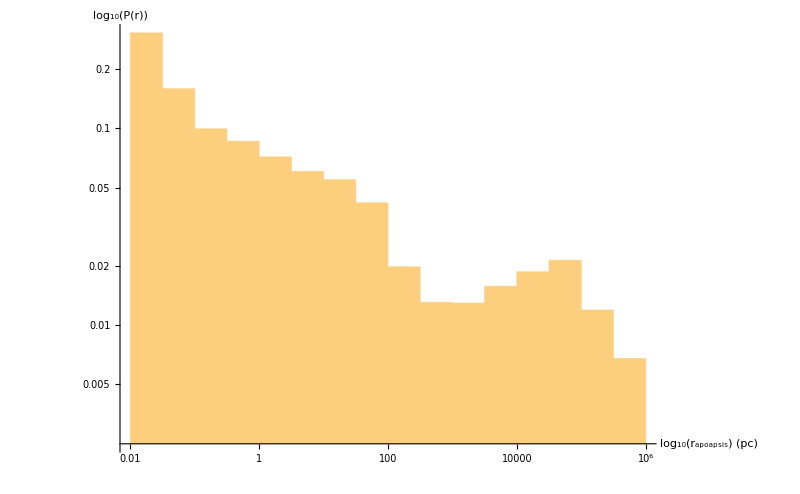

```mathematica
(*Histogram[
Flatten[unboundparts],
"Log","LogProbability",
PlotRange->All, 
ChartStyle->Lighter[Lighter[RGBColor[0.368417,0.506779,0.709798]]],
TicksStyle->fontsize,
AxesLabel->{Style["log_10(r_final) (pc)", fontsize], Style["log_10(P(r))",fontsize]},
ImageSize->800,
ImageMargins->15
]*)

Histogram[
Flatten[boundparts],
"Log","LogProbability", 
PlotRange->All, 
TicksStyle->fontsize,
AxesLabel->{Style["log_10(r_apoapsis) (pc)", fontsize], Style["log_10(P(r))",fontsize]},
ImageSize->800,
ImageMargins->15
]

(*Histogram[
{Flatten[boundparts],Flatten[unboundparts]},
"Log","LogProbability",
PlotRange->All,
TicksStyle->fontsize, 
ChartLegends->  {Style["Bound", fontsize], Style["Unbound", fontsize]}, 
AxesLabel->{Style["log_10(r) (pc)", fontsize], Style["log_10(P(r))",fontsize]}, 
ImageSize->800,
ImageMargins->15
]*)
```

## Plotting evolution of fragment position

```mathematica
boxsize=0.001;

(*ListPointPlot3D[
{allfrags, {{8,0,0}}},
PlotStyle -> {PointSize[0.012], {PointSize[0.015], Orange}},
PlotLegends->{"Fragments", "Sun"} , 
TicksStyle->13,
AxesLabel->{Style["x (kpc)",Bold, clr,15], Style["y (kpc)",Bold,clr, 15], Style["z (kpc)",Bold,clr, 15]}, 
PlotRange->{{-boxsize,boxsize},{-boxsize,boxsize},{-boxsize,boxsize}},
ImageSize->700,
ImageMargins->15,
AspectRatio->Automatic
]*)
```

```mathematica
frags = ConstantArray[1,0];
Do[
AppendTo[
frags,
With[{end=endtimes⟦i,j⟧, k=i,l=j},
If[0 ≤t-(k*10^4 yr)+(10^4 yr)≤end,
{x[t-(k*10^4 yr)+(10^4 yr)]/kpc, y[t-(k*10^4 yr)+(10^4 yr)]/kpc, z[t-(k*10^4 yr)+(10^4 yr)]/kpc}//.Flatten[solutions⟦k,l⟧],
If[t-(k*10^4 yr)+(10^4 yr)<0,
Nothing,
{x[end]/kpc, y[end]/kpc, z[end]/kpc}//.Flatten[solutions⟦k,l⟧]
]
]
]
],
{i,irange},{j,jranges⟦i⟧}
]
```

```mathematica
(*ListPointPlot3D[
{frags//.t-> (10^6 yr), {{8,0,0}}},
PlotStyle -> {PointSize[0.004], {PointSize[0.015], Orange}},
PlotLegends->{"Fragments", "Sun"} ,
PlotLabel-> Row@{Style["Time (in s): "<>TextString[N[10^5 yr]], Bold, clr, 15 ],Spacer[300]},
TicksStyle->13,
AxesLabel->{Style["x (kpc)",Bold, clr,15], Style["y (kpc)",Bold,clr, 15], Style["z (kpc)",Bold,clr, 15]},
ImageSize->700,
ImageMargins->15
]*)
(*ListPointPlot3D[
frags//.t-> (50*10^4 yr),
PlotStyle -> PointSize[0.004],
PlotLabel-> Row@{Style["Time (in s): "<>TextString[N[10^5 yr]], Bold, clr, 15 ],Spacer[300]},
TicksStyle->13,
PlotRange->{{-1,1},{-1,1},{-1,1}},
AxesLabel->{Style["x (kpc)",Bold, clr,15], Style["y (kpc)",Bold,clr, 15], Style["z (kpc)",Bold,clr, 15]},
ImageSize->700,
ImageMargins->15
]*)
```

### Exporting .gif files

```mathematica
plots0=Table[
ListPointPlot3D[
frags//.t-> time,
PlotStyle -> PointSize[0.004],
PlotLabel-> Row@{Style["Time (in s): "<>TextString[N[time]], Bold, clr, 15 ],Spacer[300]},
TicksStyle->13,
PlotRange->{{-1,1},{-1,1},{-1,1}},
AxesLabel->{Style["x (kpc)",Bold, clr,15], Style["y (kpc)",Bold,clr, 15], Style["z (kpc)",Bold,clr, 15]},
ImageSize->700,
ImageMargins->15,
AspectRatio->Automatic
],
{time,0,(5*10^5+2*10^4)yr,5*10^3 yr}
];
SetDirectory@NotebookDirectory[];
Export["1000TDEs.gif",plots0]
```

TDEs.gif

```mathematica
plots1=Table[
ListPointPlot3D[
{frags//.t-> time, {{8,0,0}}},
PlotStyle -> {PointSize[0.004], {PointSize[0.015], Orange}},
PlotLegends->{"Fragments", "Sun"} ,
PlotLabel->Row@{Style["Time (in s): "<> ScientificForm[N[time],NumberFormat->(#1<>"*10^("<>#3<>")"&)]//ToString, 
					Bold, clr, 15 ],Spacer[300]}, 
TicksStyle->13,
AxesLabel->{Style["x (kpc)",Bold, clr,15], Style["y (kpc)",Bold,clr, 15], Style["z (kpc)",Bold,clr, 15]}, 
PlotRange->{{-10,10},{-10,10},{-10,10}},
ImageSize->700,
ImageMargins->15,
AspectRatio->Automatic
],
{time,0,10^6 yr,10^4 yr}
];
SetDirectory@NotebookDirectory[];
Export["1to10-6.gif",plots1]
```

```mathematica
plots2=Table[
ListPointPlot3D[
frags//.t-> time,
PlotStyle -> PointSize[Small],
PlotLabel->Row@{Style["Time (in s): "<>TextString[N[time]], Bold, clr, 15 ],Spacer[300]}, 
TicksStyle->13,
AxesLabel->{Style["x (kpc)",Bold, clr,15], Style["y (kpc)",Bold,clr, 15], Style["z (kpc)",Bold,clr, 15]}, 
PlotRange->{{-10000,10000},{-10000,10000},{-10000,10000}},
ImageSize->700,
ImageMargins->15,
AspectRatio->Automatic
],
{time,10^6 yr,10^9 yr,10^7 yr}
];
SetDirectory@NotebookDirectory[];
Export["10-6to10-9.gif",plots2]
plots3=Table[
ListPointPlot3D[
frags//.t-> time,
PlotStyle -> PointSize[Small],
PlotLabel->Row@{Style["Time (in s): "<>TextString[N[time]], Bold, clr, 15 ],Spacer[300]}, 
TicksStyle->13,
AxesLabel->{Style["x (kpc)",Bold, clr,15], Style["y (kpc)",Bold,clr, 15], Style["z (kpc)",Bold,clr, 15]}, 
PlotRange->{{-100000,100000},{-100000,100000},{-100000,100000}},
ImageSize->700,
ImageMargins->15,
AspectRatio->Automatic
],
{time,10^8 yr,10^10 yr,10^8 yr}
];
SetDirectory@NotebookDirectory[];
Export["10-8to10-10.gif",plots3]
```

10-6to10-9.gif

10-8to10-10.gif

## Calculating Jean’s mass (M_frag)

```mathematica
rs=rsun(ms/msun)^0.8;
μ=0.5;
γ=5/3;
𝒞 = If[β ≤ 0.9, Exp[(3.1647-6.3777β + 3.1797 β^2)/(1-3.4137β+2.4616 β^2)], 1];
𝒯c= ;
𝒯f=5*10^3;
rt=(Subscript[m, hole]/ms)^(1/3)rs;
ti=π √(rt^3/(G Subscript[m, hole]));
tf=ti (𝒯c/𝒯f);
expf=(𝒯c/𝒯f)^(3/2);
nfinal=(0.5ms 𝒞)/(μ mp expf 4/3 π rs^3);
cs=√((γ kb 𝒯f)/(μ mp));
mfrag=2msun (cs/(0.2*10^5))^3(nfinal/10^3)^(-1/2);
nfrag=FullSimplify[(0.5ms 𝒞)/mfrag,Assumptions->{𝒞>0,ms>0}];(*/.{fremoved->0.01,ms->msun}*)
(*Plot[nfrag/.ms-> msun, {β, 0.5, 0.9}, AxesLabel->{"β", "n_frag"}*)
```

## Calculating nearest fragment to us

```mathematica
δr=1 kpc;
Γtde=10^-4/yr;
fracnear=BinCounts[boundparts,{{7000,9000}}]⟦1⟧/Length@boundparts //N
totalnfrag=(Length@Flatten[boundparts])/irange Γtde max
(y/. Solve[1==(totalnfrag fracnear)/((4/3 π (8 kpc+δr )^3-4/3 π (8 kpc-δr )^3)/(4/3 π y^3)),y]⟦3⟧)/pc
```

0.00347417

8923000

231.78

```mathematica
max Γtde
```

1000000

```mathematica
((totalnfrag  * fracnear2)/(π kpc^2(2π(8kpc))) * pc^3)^(-1/3)
```

559.834

```mathematica
torus =Select[bofragdraw, (#⟦1,1⟧-8)^2+(#⟦1,3⟧)^2<1&];
fracnear2=Length@torus/Length@bofragdraw //N
totalnfrag=(Length@bofragpos)/(nrealizations * irange)Γtde max;
(y/. Solve[1==(totalnfrag  * fracnear2)/(π kpc^2(2π(8kpc))/(4/3 π y^3)),y]⟦3⟧)/pc
```

0.000100863

347.293

## Counting fragments: Average, BinCounts, etc.

```mathematica
100 *BinCounts[unfragpos,{{0,17}}]⟦1⟧/Length@unfragpos //N
```

0.0267394

```mathematica
unbMWindices = Position[unfragpos, x_/; x< 17];
unboundMWvels = Extract[unfragvel,unbMWindices];
Mean[unboundMWvels]
```

6201.03

```mathematica
Mean[Table[Length@solutions⟦i⟧,{i, Length@solutions}]]
```

39407/200

```mathematica
N[39407/200]
```

197.035

```mathematica
Length@unboundindices
Length@boundindices
Length@unboundindices + Length@boundindices
Length@unfragvel
Length@bofragvel
```

188112

8923

197035

5643360

267690

```mathematica
BinCounts[boundparts,{{10^5,10^6}}]⟦1⟧/Length@boundparts //N
(*BinCounts[bofragvel,{Table[10^i,{i,-4,6}]}]
Mean[bofragvel]
Mean[unfragvel]
%/(3*10^5) //N
Max[unfragvel]
%/(3*10^5) //N*)
```

0.0186036

## Fragment mass and luminosity histogram

### Fragment masses list construction

```mathematica
fragmentmasses = Table[0,irange];
Do[mfrag= data⟦i⟧["mfrag"];
fragmentmasses⟦i⟧=mfrag,
{i,irange}]

Subscript[M, jup]= 1.9*10^30;
```

```mathematica
Max[fragmentmasses/Subscript[M, jup]]
```

21.09

```mathematica
chartColors[Histogram,$PlotTheme]
```

{RGBColor[0.97858, 0.678934, 0.157834],RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
hist1 =Directive[chartColors[Histogram,$PlotTheme]⟦4⟧,Opacity@0.6]
hist2=Directive[chartColors[Histogram,$PlotTheme]⟦5⟧,Opacity@0.6]
```

Directive[RGBColor[0.922526, 0.385626, 0.209179],Opacity[0.6]]

Directive[RGBColor[0.528488, 0.470624, 0.701351],Opacity[0.6]]

```mathematica
Histogram[fragmentmasses/Subscript[M, jup],
"Log", "LogProbability",
PlotRange->All,
ChartStyle->hist1,
GridLines->{{{13, Directive[Thick,Brown, Dashed,Opacity@1]}},{}},
Method->{"GridLinesInFront"->True},
(*ChartStyle->"Pastel",*)
FrameTicks -> Automatic,
FrameTicksStyle->Directive[Thick,fontsize],
Frame->True,
FrameLabel->{{Style["Probability",fontsize], Null},{Style["Fragment Mass (M_Jup)", fontsize], Null}},
Axes->True,
ImageSize->900,
AspectRatio->1/3,
ImageMargins-> 15,
FrameStyle->Directive[AbsoluteThickness@1, Black]
]
```

### Luminosity function setting

```mathematica
Subscript[L, sun]=3.84*10^33;
ℒ[mf_,t_]:= 7.85*10^-6*Subscript[L, sun]*(mf/(3*Subscript[M, jup]))^2.641*(t/(10^7*yr))^-1.267;
appmag[l_,d_]:= -26.832-2.5Log[10,(l/Subscript[L, sun])(au/d)^2];
```

```mathematica
λ=560 pc;
nfrags=Length@fragmentmasses;
ndraws=10000;
ages=RandomReal[{0,10^10 yr},{ndraws,nfrags}];
ds=nfrags^(1/3) λ RandomReal[{0,1},{ndraws,nfrags}]^(1/3);
mfrags=ConstantArray[fragmentmasses,ndraws];

lum=ℒ[mfrags,ages];
mags=appmag[lum,ds];
mmag=Min/@mags;

brightest={mmag,#[[3]][[Position[#[[2]],#[[1]]][[1,1]]]]&/@({mmag,mags,ds}ᵀ)/pc}ᵀ;
mbrightest=Median[brightest⟦All,1⟧];
```

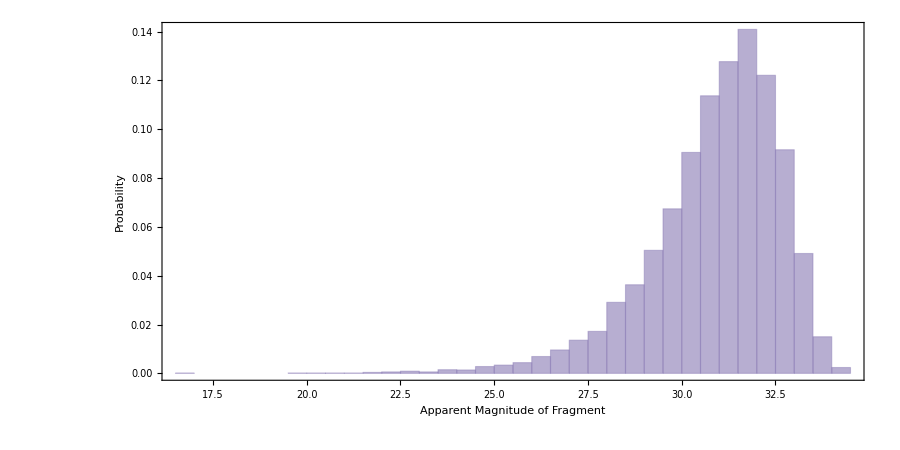

```mathematica
Histogram[brightest[[All,1]],
Automatic,"Probability",
ChartStyle->hist2,
PlotRange->All,
FrameTicks -> Automatic,
FrameTicksStyle->fontsize,
Frame->True,
FrameLabel->{{Style["Probability",fontsize], Null},{Style["Apparent Magnitude of Fragment", fontsize], Null}},
Axes->True,
ImageSize->900,
AspectRatio->1/2,
ImageMargins-> 15,
FrameStyle->Directive[AbsoluteThickness@1, Black]
]
```

```mathematica
mbrightest
```

31.1867

```mathematica
Table[Quantile[brightest⟦All,1⟧,10^-i],{i,2}]
```

{28.6422,25.4058}

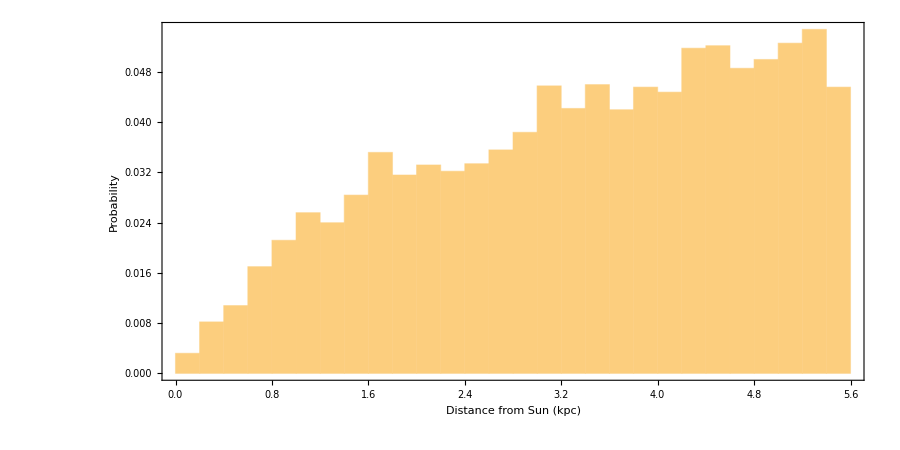

```mathematica
Histogram[Select[brightest,#⟦1⟧<mbrightest&]⟦All,2⟧/1000,
Automatic,"Probability",
PlotRange->All,
FrameTicks -> Automatic,
FrameTicksStyle->fontsize,
Frame->True,
FrameLabel->{{Style["Probability",fontsize], Null},{Style["Distance from Sun (kpc)", fontsize], Null}},
Axes->True,
ImageSize->900,
AspectRatio->1/2,
ImageMargins-> 15,
FrameStyle->Directive[AbsoluteThickness@1, Black]
]
```

## Other luminosity calculations

```mathematica
times =RandomReal[{1,max},Length@fragmentmasses];
luminosities = ℒ[#⟦1⟧,#⟦2⟧]&/@Transpose[{fragmentmasses,times}];
```

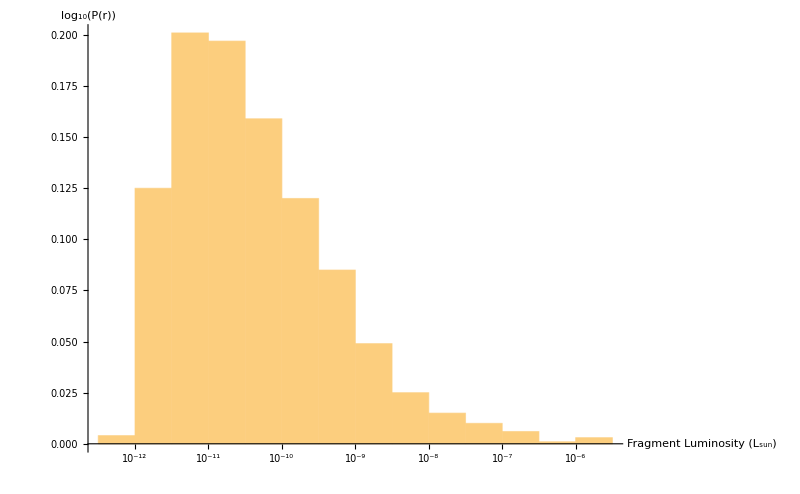

```mathematica
Histogram[
luminosities/Subscript[L, sun],
"Log","Probability", 
PlotRange->All, 
TicksStyle->fontsize,
AxesLabel->{Style["Fragment Luminosity (L_sun)", fontsize], Style["log_10(P(r))",fontsize]},
ImageSize->800,
ImageMargins->15,
FrameStyle->Directive[AbsoluteThickness@1, Black]
]
```

```mathematica
Table[Select[boundindices,#⟦1⟧==star&],{star,1000}];
drawnlpind=RandomChoice[#]&/@Select[%, #≠ {}&];
```

```mathematica
lumpositions = ConstantArray[0,1000];
Do[
posindex = Total[jranges⟦;;i⟧];
distance = Norm[bofragdraw⟦posindex,1⟧-{8,0,0}]*kpc;
lumpositions⟦i⟧=distance,
{i,1000}]
apparentmagnitudes = appmag[#⟦1⟧,#⟦2⟧]&/@Transpose[{luminosities,lumpositions}];
```

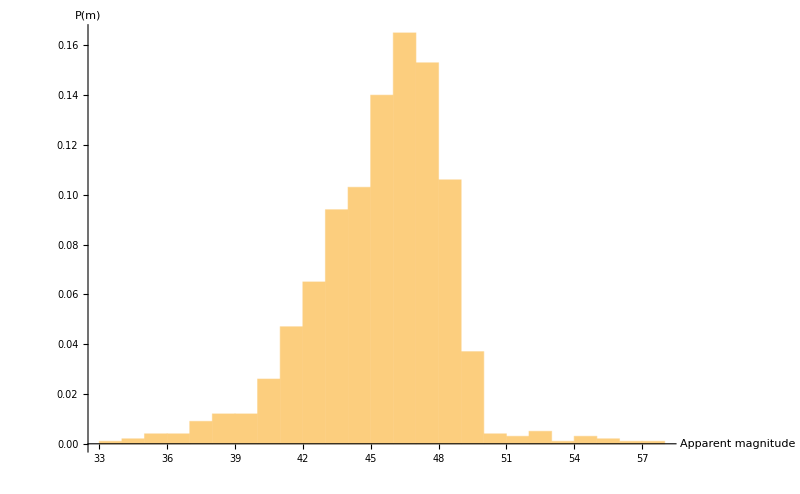

```mathematica
Histogram[
apparentmagnitudes,
Automatic,"Probability", 
PlotRange->All, 
TicksStyle->fontsize,
AxesLabel->{Style["Apparent magnitude", fontsize], Style["P(m)",fontsize]},
ImageSize->800,
ImageMargins->15,
FrameStyle->Directive[AbsoluteThickness@1, Black]
]
```

## Density Plots

### Random realizations

```mathematica
nrealizations=30;
ki=0;
generateBoundFragPositions:=With[{},
randfrags = ConstantArray[1,Length@boundindices];
Do[
bi=boundindices⟦k⟧;
{i,j}=bi;
ki++;
randfrags⟦k⟧=With[{θ=RandomReal[{0,2π}]},Evaluate[{{Norm[{x[t],y[t]}] Cos[θ], Norm[{x[t],y[t]}] Sin[θ], z[t]}/kpc, Norm[{x'[t], y'[t], z'[t]}]/100000}/.Flatten[solutions⟦i,j⟧]/.{t -> endtimes⟦i,j⟧RandomReal[]}]];
,{k,Length@boundindices}
];
Return@randfrags
]
ProgressIndicator[Dynamic[ki], {1,nrealizations Length@boundindices}]
bofragdraw=Flatten[Table[generateBoundFragPositions,{nrealizations}],1];

ui=0;
generateUnboundFragPositions:=With[{},
randfrags = ConstantArray[1,Length@unboundindices];
Do[
bi=unboundindices⟦k⟧;
{i,j}=bi;
ui++;
randfrags⟦k⟧=Evaluate[{{x[t], y[t], z[t]}/kpc, Norm[{x'[t], y'[t], z'[t]}]/100000}/.Flatten[solutions⟦i,j⟧]/.{t -> endtimes⟦i,j⟧RandomReal[]}]
,{k,Length@unboundindices}
];
Return@randfrags
]
ProgressIndicator[Dynamic[ui], {1,nrealizations Length@unboundindices}]
unfragdraw=Flatten[Table[generateUnboundFragPositions,{nrealizations}],1];
```

### Defining position and velocity objects for bound/unbound fragments

```mathematica
bofragpos = Norm/@(bofragdraw⟦All,1⟧);
bofragvel = bofragdraw⟦All,2⟧;

unfragpos = Norm/@(unfragdraw⟦All,1⟧);
unfragvel = unfragdraw⟦All,2⟧;
```

### Histograms for position and velocity

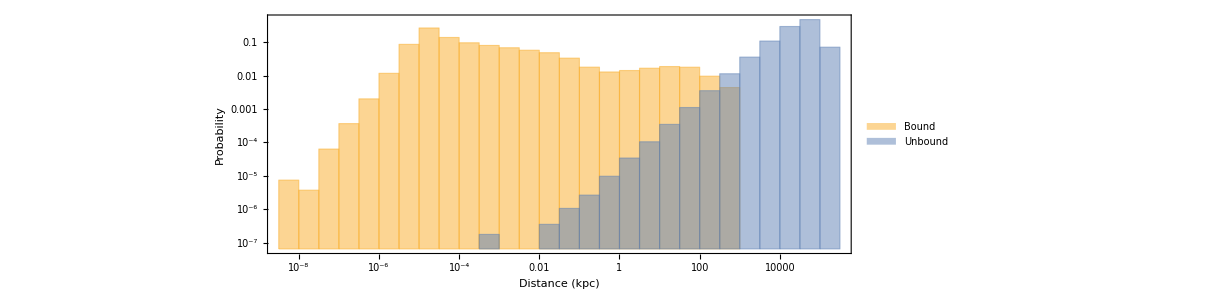

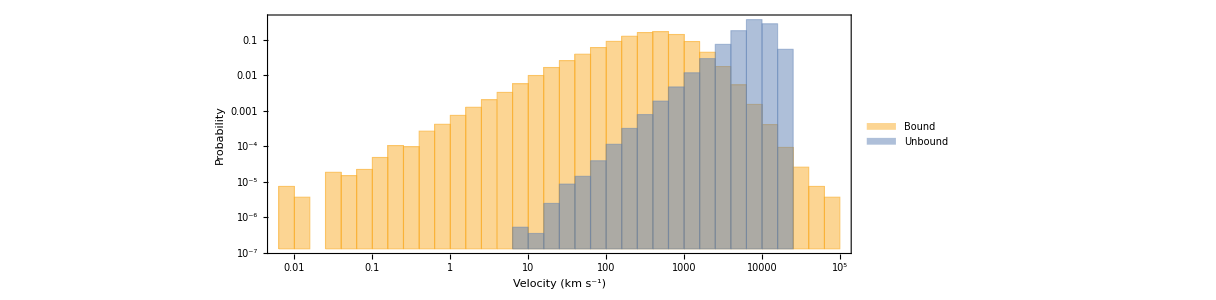

```mathematica
Histogram[
{bofragpos,unfragpos},
"Log","LogProbability",
ChartLegends -> Placed[SwatchLegend[{"Bound", "Unbound"},LabelStyle-> {GrayLevel[0.25], fontsize}, LegendLayout->"Row"], {{0.5,0.9},{0.5,0.5}}],
PlotRange->All,
FrameTicks -> All,
FrameTicksStyle->fontsize,
Frame->True,
FrameLabel->{{Style["Probability",fontsize], Null},{Style["Distance (kpc)", fontsize], Style["Fragment Position", fontsize]}},
Axes->True,
ImageSize->900,
AspectRatio->1/3,
ImageMargins-> 15,
FrameStyle->Directive[AbsoluteThickness@1, Black]
]

Histogram[
{bofragvel,unfragvel},
"Log","LogProbability",
ChartLegends -> Placed[SwatchLegend[{"Bound", "Unbound"},LabelStyle-> {GrayLevel[0.25], fontsize}, LegendLayout->"Row"], {{0.4,0.9},{0.5,0.5}}],
PlotRange->All,
FrameTicks -> All,
FrameTicksStyle->fontsize,
Frame->True,
FrameLabel->{{Style["Probability",fontsize], Null},{Style["Velocity (km s^-1)", fontsize], Style["Fragment Velocity", fontsize]}},
Axes->True,
ImageSize->900,
AspectRatio->1/3,
ImageMargins-> 15,
FrameStyle->Directive[AbsoluteThickness@1, Black]
]
```

### Calculating angular distribution

```mathematica
nearbofragdraw = Select[bofragdraw, 0.1<Norm[#⟦1⟧]<√2 20&];
nearunfragdraw = Select[unfragdraw, 0.1<Norm[#⟦1⟧]<√2 20&];
```

```mathematica
angles=π/2-ArcTan[Norm[{#⟦1⟧,#⟦2⟧ }], Abs[#⟦3⟧]]&/@nearbofragdraw⟦All,1⟧;
dx=(π/2)/10;
xs=Range[0,π/2+dx,dx];
bcs=BinCounts[angles,{xs}];
angleticks = Table[Simplify[Pi/16*x], {x, 0,8,1 }];
```

#### PDF Function plot

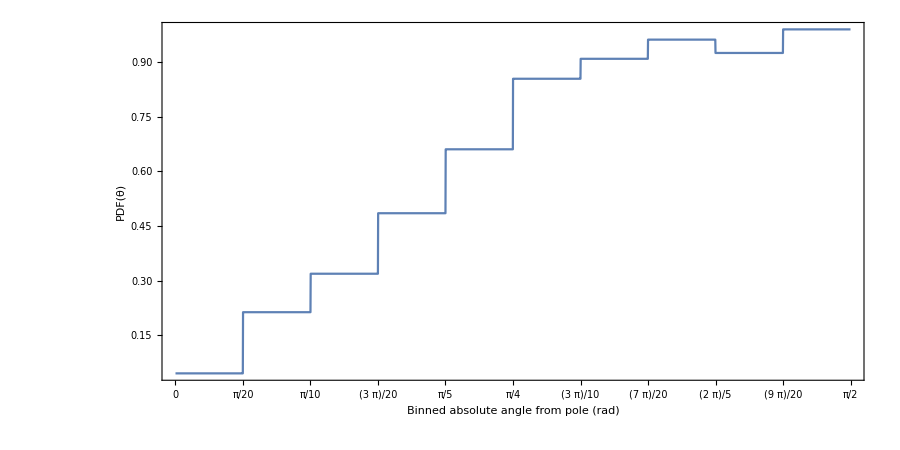

```mathematica
xmarks = MovingAverage[xs,2]-dx/2;
ymarks = Join[{bcs⟦1⟧},(bcs/(Total[bcs]*dx))⟦;;Length[bcs]-1⟧];
f=Interpolation[Transpose@{xmarks,ymarks},InterpolationOrder->0];
Plot[f[t],{t,Min@xmarks,Max@xmarks},
Frame -> {{True, False},{True, False}},
FrameTicks->{xs, All},
PlotRange->All,
FrameTicksStyle->fontsize-2,
FrameLabel->{Style["Binned absolute angle from pole (rad)", fontsize],Style["PDF(θ)",fontsize]},
ImageSize->900,
AspectRatio->1/2,
ImageMargins-> 15
]
```

#### Random angle calculations...

```mathematica
f[9π/20+(π/30)] //N
```

0.0448495

```mathematica
N[π/20]
```

0.15708

```mathematica
N[π/8]
```

0.392699

```mathematica
NIntegrate[f[t],{t,0, π/2}] //N
```

0.376618

0.35277

0.270611

```mathematica
(*ListPlot[{Sort@angles,(Range@Length@angles)/(Length@angles)}ᵀ,Joined->True]*)
```

```mathematica
(*Plot[(1-Cos[θ]), {θ,0,π/2}]*)
```

```mathematica
vol[x_] := 1-Cos[x];
dstat=Max[#⟦2⟧-vol[#⟦1⟧]&/@Transpose[{Sort@angles,(Range@Length@angles)/(Length@angles)}]]
Solve[√(-1/2 Log[α/2])Sqrt[1/(Length@angles)]==dstat,α]
```

0.0207999

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{α→2.55021×10^-8}}

#### CDF Function plot

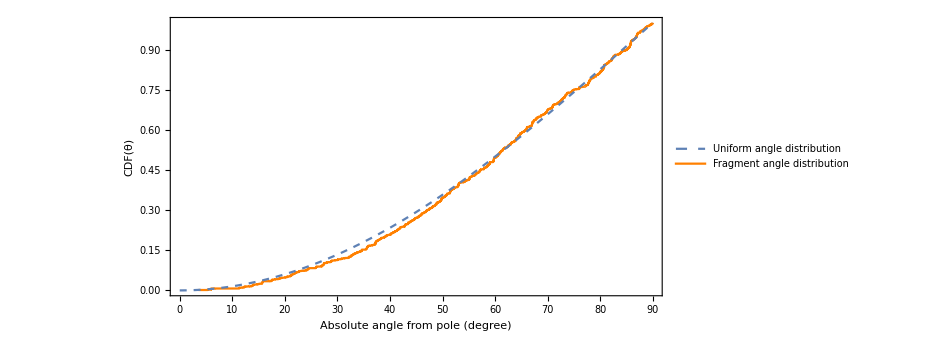

```mathematica
rads=180/π;
cdflegend = Placed[
LineLegend[
{Directive[clr,Dashed], Orange},
{"Uniform angle distribution","Fragment angle distribution"},
LabelStyle-> {Black, fontsize-4}
],{{0.05,0.8},{0,0}}];
Legended[Show[ListPlot[{Sort[angles*rads],(Range@Length@angles)/(Length@angles)}ᵀ,Joined->True, PlotStyle->Orange],
Plot[(1-Cos[θ/rads]), {θ,0,90}, PlotStyle->Dashed],
PlotRangePadding-> 0,
Frame -> True,
FrameTicks->{{Automatic, Automatic},{Range[0,90,10], Automatic}},
PlotRange->All,
FrameTicksStyle->fontsize-2,
FrameLabel->{Style["Absolute angle from pole (degree)", fontsize],Style["CDF(θ)",fontsize]},
ImageSize->700,
AspectRatio->1/2,
ImageMargins-> 15,
FrameStyle->Directive[AbsoluteThickness@1, Black]
], cdflegend]
```

### Spatial density plot - BOUND, NEAR GALACTIC CENTER

```mathematica
pr=2; (*plot range*)
ptsize=0.1;
bominvel=Min[bofragvel];
bomaxvel=1000;
bocolorf = Function[Blend[{Red,Blue},(#-bominvel)/(bomaxvel-bominvel)]];
g3=Graphics[{Antialiasing->True,Blend[{Red,Blue},(#⟦2⟧-bominvel)/(bomaxvel-bominvel)],Opacity@0.75,Disk[{#⟦1,1⟧,#⟦1,3⟧},0.25ptsize]}&/@nearbofragdraw,Frame->True,PlotRange->{{-pr,pr},{0,pr}},PlotRangeClipping->True];
bovellegend = Placed[BarLegend[
{bocolorf, {bominvel, bomaxvel}},
LegendLabel->Style["Fragment velocity (km s^-1)", GrayLevel[0.25]], 
LegendFunction->"Panel",
LabelStyle-> {fontsize-5}
], {{1.01,0.7},{0,1}}];

Show[
Legended[{g3}, bovellegend],
FrameTicksStyle->fontsize-2,
FrameLabel->{Style["x (kpc)", fontsize],Style["z (kpc)",fontsize]},
ImageSize-> 1000,
ImageMargins -> 10
]
```

### Spatial density plot - MW FRAGMENTS (ound and some unbound)

```mathematica
pr=7.5; (*plot range*)
ptsize=0.1;
minvel=Min[nearunfragdraw⟦All,2⟧~Join~nearbofragdraw⟦All,2⟧];
maxvel=Max[nearunfragdraw⟦All,2⟧~Join~nearbofragdraw⟦All,2⟧];
plotbofrag = Select[nearbofragdraw, (0.01pr≤ #⟦1,3⟧≤pr) && (-2pr≤#⟦1,1⟧≤2pr )&];
plotunfrag = Select[nearunfragdraw, (0.01pr≤ #⟦1,3⟧≤pr) && (-2pr≤#⟦1,1⟧≤2pr) &];
colorf = Function[Blend[{Red,Blue},(#-minvel)/(maxvel-minvel)]];
g1=Graphics[{Antialiasing->True,Blend[{Red,Blue},(#⟦2⟧-minvel)/(maxvel-minvel)],Opacity@0.75,Disk[{#⟦1,1⟧,#⟦1,3⟧},ptsize]}&/@plotunfrag,Frame->True,PlotRange->{{-2pr,2pr},{0,pr}},PlotRangeClipping->True];
g2=Graphics[{Antialiasing->True,Blend[{Red,Blue},(#⟦2⟧-minvel)/(maxvel-minvel)],Opacity@1,Circle[{#⟦1,1⟧,#⟦1,3⟧},0.5ptsize]}&/@plotbofrag,Frame->True,PlotRange->{{-2pr,2pr},{0,pr}},PlotRangeClipping->True];

sunpoint = Graphics@{FaceForm@Yellow,EdgeForm[Directive[Black,AbsoluteThickness@1.5]], Polygon[Riffle[CirclePoints@5,(RotationTransform[360 °/10][#]&/@(0.35*CirclePoints@5))]]};
gsun=Graphics[{FaceForm@Yellow,EdgeForm[Directive[Black,AbsoluteThickness@1.5]], Translate[Polygon[0.5Riffle[CirclePoints@5,(RotationTransform[360 °/10][#]&/@(0.35*CirclePoints@5))]],{8,0}]}, PlotRangeClipping->False];

markers = {{Graphics[Circle[]], 0.05}, {Graphics[Disk[]], 0.06}, {sunpoint,15}};
glegend = Placed[PointLegend[
{None, None,None},
{"Bound fragments","Unbound fragments", "Sun"},
LabelStyle-> {GrayLevel[0.25], 13},
LegendMarkers->markers,
LegendLayout->"Row",
LegendFunction->"Panel"
],{{0.01,1.00001},{0,0}}];

vellegend = Placed[BarLegend[
{colorf, {minvel, maxvel}},
LegendLabel->Style["Fragment velocity (km s^-1)", GrayLevel[0.25]], 
LegendFunction->"Panel",
LabelStyle-> {fontsize-5}
], {{1.01,0.7},{0,1}}];

Show[
(*Legended[Legended[{g2,g1,gsun},glegend], vellegend],*)
Legended[{g2,g1,gsun},{glegend, vellegend}],
FrameTicksStyle->fontsize-2,
FrameLabel->{Style["x (kpc)", fontsize],Style["z (kpc)",fontsize]},
PlotRangeClipping->False,
FrameStyle->Directive[AbsoluteThickness@1, Black],
ImageSize-> 1000,
ImageMargins -> 10
]
```

### Spatial density plot - S-Z PLANE

```mathematica
pr2= 30;
plotbofragsz = Select[nearbofragdraw, (0.01pr≤ Abs[#⟦1,3⟧]≤pr2) && (0.01pr≤Sqrt[(#⟦1,1⟧)^2+(#⟦1,2⟧)^2]≤ pr2 )&];
plotunfragsz = Select[nearunfragdraw, (0.01pr≤ Abs[#⟦1,3⟧]≤pr2) && (0.01pr≤Sqrt[(#⟦1,1⟧)^2+(#⟦1,2⟧)^2]≤pr2) &];g3=Graphics[{Antialiasing->True,Blend[{Red,Blue},(#⟦2⟧-minvel)/(maxvel-minvel)],Opacity@0.75,Disk[{Sqrt[(#⟦1,1⟧)^2+(#⟦1,2⟧)^2],Abs[#⟦1,3⟧]},ptsize]}&/@plotunfragsz,Frame->{{True, False},{True, False}},PlotRange->{{0,pr2},{0,pr2}},PlotRangeClipping->True];
g4=Graphics[{Antialiasing->True,Blend[{Red,Blue},(#⟦2⟧-minvel)/(maxvel-minvel)],Opacity@1,Circle[{Sqrt[(#⟦1,1⟧)^2+(#⟦1,2⟧)^2],Abs[#⟦1,3⟧]},0.5ptsize]}&/@plotbofragsz,Frame->{{True, False},{True, False}},PlotRange->{{0,pr2},{0,pr2}},PlotRangeClipping->True];

glegend2 = Placed[PointLegend[
{None,None,None},
{"Bound fragments","Unbound fragments", "Sun"},
LabelStyle-> {GrayLevel[0.25], 13},
LegendMarkers-> markers, 
LegendLayout->"Row",
LegendFunction->"Panel"
],{{0.01,0.95},{0,0}}];
Show[
Legended[Legended[{g3,g4,gsun},glegend2], vellegend],
FrameTicksStyle->fontsize-2,
FrameLabel->{Style["s = √(x^2) (kpc)", fontsize],Style["|z| (kpc)",fontsize]},
PlotRangeClipping->False,
FrameStyle->Directive[AbsoluteThickness@1, Black],
ImageSize-> 800,
ImageMargins -> 10
]
```

-Graphics-

### Another effort at a spatial density plot

```mathematica
densitytab=ParallelTable[(Length@Select[fragdraw,Norm[{Norm[#⟦1;;2⟧]-s,#⟦3⟧-z}]<Norm[{s,z}]/5&])/(2 π^2 s(Norm[{s,z}]/5)^2),{s,1,100,4*2.4},{z,1,100,4*2.4}];
```

```mathematica
Max[densitytab*10^3]//N
```

100688.

```mathematica
(*Log10@densitytab*)
```

```mathematica
(*Reverse[Log10@densitytab,2]*)
```

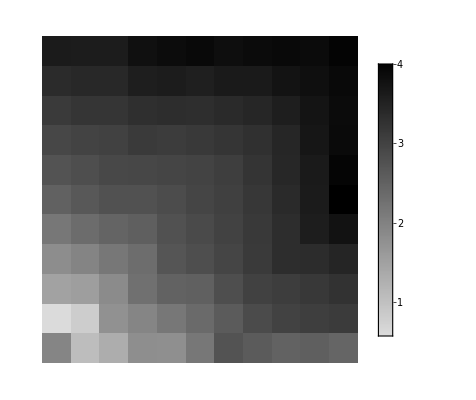

```mathematica
sticks = Transpose[{Range@(Length@Range[1,100,4*2.4]),Range[1,100,4*2.4]}];
zticks = Transpose[{Range@(Length@Range[1,100,4*2.4]),Range[1,100,4*2.4]}];
ArrayPlot[Reverse[Log10@densitytab,1],PlotLegends->Automatic(*, ColorFunction->(ColorData["TemperatureMap"][#3]&)*), FrameTicks-> {zticks,sticks}]
```

```mathematica
sunfragdraw = Select[fragdraw,Norm[{#⟦1⟧-8,#⟦2⟧}]<1&];
((Length@sunfragdraw)/(16 π^2)*10^3)^(-1/3)//N
```

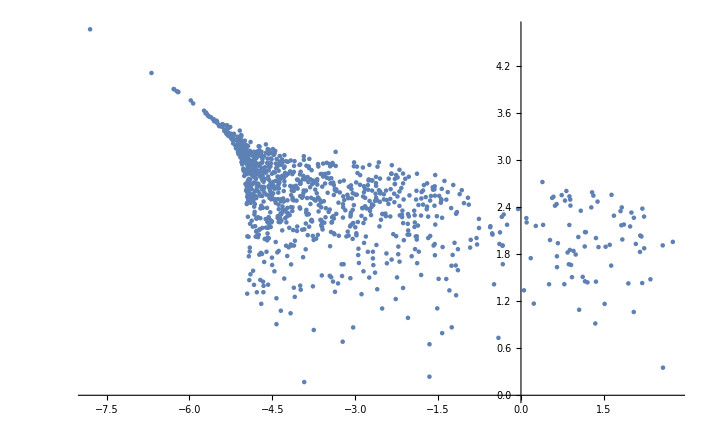

```mathematica
ListPlot[Log10@Transpose[{fragposdraw, fragveldraw}]⟦;;1000⟧]
```

### Histogram of error

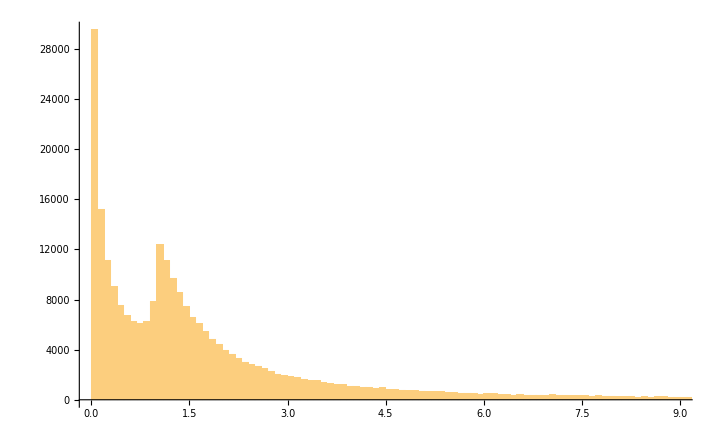

```mathematica
Histogram[Sqrt[(2*G*(4.0* 10^6 msun))/(fragposdraw * kpc)]/(fragveldraw*10^5), {0.1}]
```